# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.908609466019007×10^9

#### 変数

```mathematica
date="20231010"
```

20231010

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231010.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231010.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

21124901 293477497 9943356563 log-20231010.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=ci.P~5

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

2922727

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{2922727,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90588×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-10-09T15:00:01Z
log.ci0001.aws.wa03.yobi
66.249.71.8
host":"-
user":"-
3.90588×10^9
method":"GET
https://cir.nii.ac.jp/crid/1583387450178802304
code":"200
size":"12015
-
agent":"Googlebot/2.1 (+http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.71.8\"
request_time":"0.028
upstream_response_time":"0.027"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "10.2494".

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

StringTake::take: Cannot take positions 1 through 19 in "Graphics".

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

StringTake::take: Cannot take positions 1 through 19 in "css".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-10-09T15:00:01Z
log.ci0001.aws.wa03.yobi
66.249.79.5
host":"-
user":"-
3.90588×10^9
method":"GET
https://cir.nii.ac.jp/crid/1580291611848561280
code":"200
size":"12093
-
agent":"Googlebot/2.1 (+http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.79.5\"
request_time":"0.026
upstream_response_time":"0.027"}
1580291611848561280
toCRID[-]

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=cs.R=.P=

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

28196

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{28196,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{28196,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"mstshash=Administr

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-10-10T00:00:43.095870092+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-10-09T15:28:15Z
log.cs0002.ksw.wa01.yobi
35.213.23.14
stream":"stdout
user":"-
3.90589×10^9
date_time":"09/Oct/2023:15:28:14 +0000
https://jupyter.cs.rcos.nii.ac.jp/hub/home
method":"GET
code":"200
https://openidp.nii.ac.jp/idp/profile/SAML2/Redirect/SSO?execution=e1s3
agent":"Mozilla/5.0 (X11; Linux x86_64) AppleWebKit/537.36 (KHTML, like Gecko) HeadlessChrome/88.0.4324.150 Safari/537.36
size":"12775
hostname":"fluentd-bllnp"}

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=la.T~ea.A~hc.A~go.A~bot.P~api

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

11579

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{11579,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0001.aws.wa01.yobi,11575},{log.la0002.aws.wa01.yobi,4}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{11575,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{4,12}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{0}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2023-10-09T15:00:00Z
log.la0001.aws.wa01.yobi
{"user":"1dbf862fd81df075dbe099e0a3517cef88b0bd0ccc5195ad6a800bac6159a1a7
date_time":"10/Oct/2023:00:00:00 +0900
method":"GET
path":"/pluginfile.php/73176/mod_scorm/content/1/text/img/tsubasa05.png
code":"200
size":"13337
referer":"https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15
http_x_forwarded_for":"153.246.186.69
session_id":"1d805ha9nda24m93q3qscnuhh1"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{11575,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

2023-10-09T22:38:24Z
log.la0002.aws.wa01.yobi
{"user":"-
date_time":"09/Oct/2023:22:38:24 +0000
method":"GET
path":"/robots.txt
code":"404
size":"1947
referer":"-
agent":"Mozilla/5.0 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)
http_x_forwarded_for":"66.249.71.69
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{4,12}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{0}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{11579,12}

```mathematica
strSplt1R["la"][[1]]
```

{2023-10-09T15:00:00Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"153.246.186.69,size":"13337,method":"GET,date_time":"10/Oct/2023:00:00:00 +0900,code":"200,path":"/pluginfile.php/73176/mod_scorm/content/1/text/img/tsubasa05.png,{"user":"1dbf862fd81df075dbe099e0a3517cef88b0bd0ccc5195ad6a800bac6159a1a7,session_id":"1d805ha9nda24m93q3qscnuhh1"},referer":"https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/02_03.html,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.90588×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2023-10-09T15:00:00Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"153.246.186.69
size":"13337
method":"GET
3.90592×10^9
code":"200
https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/img/tsubasa05.png
{"user":"1dbf862fd81df075dbe099e0a3517cef88b0bd0ccc5195ad6a800bac6159a1a7
session_id":"1d805ha9nda24m93q3qscnuhh1"}
https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{11579,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2023-10-09T15:00:00Z
log.la0001.aws.wa01.yobi
153.246.186.69
size":"13337
method":"GET
3.90592×10^9
code":"200
https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/img/tsubasa05.png
{"user":"1dbf862fd81df075dbe099e0a3517cef88b0bd0ccc5195ad6a800bac6159a1a7
session_id":"1d805ha9nda24m93q3qscnuhh1"}
https://lms.nii.ac.jp/pluginfile.php/73176/mod_scorm/content/1/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=wk.P~4.A~bot

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

424

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{424,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{424,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-10-09T15:12:36+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.90589×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-10-09T17:54:28Z
log.wk1001.oci.wa01.yobi
201.43.63.199
user":"-
method":"GET
3.9059×10^9
code":"200
https://jdcat.jsps.go.jp/get_search_setting
size":"165
http_x_forwarded_for":"201.43.63.199"}
https://jdcat.jsps.go.jp/search?page=1&search_type=1&q=%E7%B2%BE%E7%A5%9E%E5%88%86%E6%9E%90%E5%AD%A6&sort=wtl&size=20
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64; rv:109.0) Gecko/20100101 Firefox/118.0

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
Timing[(strSplt1CCCC[3]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{33.3758,{2951347}}

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{32.4001,{2962926}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{2962926}

### ckanデータの処理(基盤全て)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{2962926}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

193

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

193

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{2962926}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

11

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

11

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

204

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

204

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{32.2083,{2922727,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-10-09T17:39:25Z
log.ci0001.aws.wa02.yobi
100.0.109.139
host":"-
user":"-
3.90589×10^9
method":"GET
https://cir.nii.ac.jp/crid/1570009750256242176
code":"200
size":"12343
https://scholar.google.com/scholar_lookup?journal=Science+and+Psychoanalysis&title=The+core+problem+in+depression:+The+cognitive+triad&author=AT+Beck&volume=17&publication_year=1970&pages=47-55&
agent":"Mozilla/5.0 (iPhone; CPU iPhone OS 16_6_1 like Mac OS X) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Mobile/15E148 Safari/604.1
http_x_forwarded_for":"\"100.0.109.139\"
request_time":"0.069
upstream_response_time":"0.069"}
1570009750256242176
toCRID[https://scholar.google.com/scholar_lookup?journal=Science+and+Psychoanalysis&title=The+core+problem+in+depression:+The+cognitive+triad&author=AT+Beck&volume=17&publication_year=1970&pages=47-55&]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{2922727}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690857923906760064,1690013498972404864,1690857923900576640,1690576448922281728,1690294973950899968,1690576448934541440,1690294973953361024,1690013498980300544,1690013498970963584,1690013498974911744,1690294973953499136,1690013498969192960,1690013498966473472,1690013498976547712,1690857923906769792,1690857923906769792,1690013498976670592,1690857923901247488,1690294973947274112,1690013498976893568,1690576448924852224,1690857977695145728,1690013498976913152,1690013498970619008,1690013498976413568,1690013498976463232,1690013498976413568,1690013498976413568,1690013498976413568,1690013498965603072,1690576448928296192,1690857923900586624,1690013498976675840,1690013498970072448,1690576448930253056,1690857923900834048,1690576448929910016,1690857923905720576,1690294973956788480,1690857923895018112,1690294973952647424,1690013498965653888,1690576448932470400,1690857923895018112,1690857923909585408,1690857923904386176,1690294973957307904,1690576448925019008,1690294973952875904,1690857923898789632,1690294973952875904,1690013498971737344,1690013498969107200,1690013498969107200,1690857999361769088,1690013498974186880,1690013498980439168,1690013498964838144,1690576448922646016,1690294973953347840,1690857923904386176,1690013498980300544,1690013498980300544,1690013498980300544,1690013498980300544,1690294973944030592,1690013498965105792,1690857923906415360,1690576448920589568,1690294973951018112,1690013498977062528,1690576448932470400,1690857923895229440,1690857923900730752,1690013498969107200,1690013498968639488,1690013498966314880,1690857923906365056,1690013498975765248,1690013498972088192,1690294973941437184,1690013498976971264,1690294973953559168,1690013498976988032,1690013498970759936,1690013498969872384,1690857923900730752,1690013498969653248,1690857923898598784,1690294973952347008,1690294973947091200,1690013498977062528,1690576448924126976,1690857923900729088,1690294973943406464,1690013498965653888,1690013498979995520,1690576448918044288,1690576448931816704,1690576448932977792,1690576448933292160,1690294973953659392,1690013498968709120,1690013498977767936,1690294973947884672,1690294973943660544,1690013498968709120,1690857923899651200,1690857923907126400,1690294973947166848,1690013498967245824,1690013498976715264,1690013498980733568,1690857923896633856,1690013498971679744,1690857977695145728,1690576448925155328,1690857923905597824,1690857923905597824,1690013498971559424,1690294973943660544,1690013498966020480,1690294973952655616,1690013498976558080,1690013498970769536,1690013498968709120,1690013498980761472,1690857923897998336,1690294973957407104,1690857923910070656,1690576448928548480,1690857923905720576,1690294973947311744,1690857923910793472,1690013498965667072,1690013498964622464,1690013498966568704,1690013498980182784,1690294973941657088,1690576448924855040,1690013498969020544,1690013498975041152,1690013498967202176,1690013498975967872,1690857923904386176,1690294973952610560,1690294973942252032,1690013498965673600,1690576448923818752,1690857923910326656,1690576448922902656,1690013498974922112,1690013498976358784,1690576448931157760,1690857923905943808,1690576448920591360,1690013498981660160,1690576448925279360,1690576448919948160,1690576448925250688,1690857923897871744,1690857923911661312,1690576448925167872,1690013498966840448,1690013498967982592,1690857923907285760,1690857923910750464,1690576448934831744,1690857923901866624,1690013498971476864,1690013498977526144,1690857923911907840,1690013498975782528,1690857923896116352,1690576448926477184,1690013498980300544,1690294973946921728,1690576448922190464,1690013498966840448,1690013498981456384,1690013498965964800,1690576448933795840,1690857923896116352,1690013498979871232,1690294973944403072,1690013498965064704,1690576448918120960,1690576448925123200,1690576502718063872,1690857923911505152,1690576502718065536,1690013498966606208,1690576448923163904}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690294973953361024,1690294973953361024,1690294973953361024,1690013498974911744,1690576448932470400,1690576448932470400,1690294973952875904,1690857923900730752,1690294973953559168,1690013498976988032,1690013498976358784}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964622464,1690013498964838144,1690013498965064704,1690013498965105792,1690013498965603072,1690013498965653888,1690013498965667072,1690013498965673600,1690013498965964800,1690013498966020480,1690013498966314880,1690013498966473472,1690013498966568704,1690013498966606208,1690013498966840448,1690013498967202176,1690013498967245824,1690013498967982592,1690013498968639488,1690013498968709120,1690013498969020544,1690013498969107200,1690013498969192960,1690013498969653248,1690013498969872384,1690013498970072448,1690013498970619008,1690013498970759936,1690013498970769536,1690013498970963584,1690013498971476864,1690013498971559424,1690013498971679744,1690013498971737344,1690013498972088192,1690013498972404864,1690013498974186880,1690013498974911744,1690013498974922112,1690013498975041152,1690013498975765248,1690013498975782528,1690013498975967872,1690013498976358784,1690013498976413568,1690013498976463232,1690013498976547712,1690013498976558080,1690013498976670592,1690013498976675840,1690013498976715264,1690013498976893568,1690013498976913152,1690013498976971264,1690013498976988032,1690013498977062528,1690013498977526144,1690013498977767936,1690013498979871232,1690013498979995520,1690013498980182784,1690013498980300544,1690013498980439168,1690013498980733568,1690013498980761472,1690013498981456384,1690013498981660160,1690294973941437184,1690294973941657088,1690294973942252032,1690294973943406464,1690294973943660544,1690294973944030592,1690294973944403072,1690294973946921728,1690294973947091200,1690294973947166848,1690294973947274112,1690294973947311744,1690294973947884672,1690294973950899968,1690294973951018112,1690294973952347008,1690294973952610560,1690294973952647424,1690294973952655616,1690294973952875904,1690294973953347840,1690294973953361024,1690294973953499136,1690294973953559168,1690294973953659392,1690294973956788480,1690294973957307904,1690294973957407104,1690576448918044288,1690576448918120960,1690576448919948160,1690576448920589568,1690576448920591360,1690576448922190464,1690576448922281728,1690576448922646016,1690576448922902656,1690576448923163904,1690576448923818752,1690576448924126976,1690576448924852224,1690576448924855040,1690576448925019008,1690576448925123200,1690576448925155328,1690576448925167872,1690576448925250688,1690576448925279360,1690576448926477184,1690576448928296192,1690576448928548480,1690576448929910016,1690576448930253056,1690576448931157760,1690576448931816704,1690576448932470400,1690576448932977792,1690576448933292160,1690576448933795840,1690576448934541440,1690576448934831744,1690576502718063872,1690576502718065536,1690857923895018112,1690857923895229440,1690857923896116352,1690857923896633856,1690857923897871744,1690857923897998336,1690857923898598784,1690857923898789632,1690857923899651200,1690857923900576640,1690857923900586624,1690857923900729088,1690857923900730752,1690857923900834048,1690857923901247488,1690857923901866624,1690857923904386176,1690857923905597824,1690857923905720576,1690857923905943808,1690857923906365056,1690857923906415360,1690857923906760064,1690857923906769792,1690857923907126400,1690857923907285760,1690857923909585408,1690857923910070656,1690857923910326656,1690857923910750464,1690857923910793472,1690857923911505152,1690857923911661312,1690857923911907840,1690857977695145728,1690857999361769088}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964622464→True,1690013498964838144→True,1690013498965064704→True,1690013498965105792→True,1690013498965603072→True,1690013498965653888→True,1690013498965667072→True,1690013498965673600→True,1690013498965964800→True,1690013498966020480→True,1690013498966314880→True,1690013498966473472→True,1690013498966568704→True,1690013498966606208→True,1690013498966840448→True,1690013498967202176→True,1690013498967245824→True,1690013498967982592→True,1690013498968639488→True,1690013498968709120→True,1690013498969020544→True,1690013498969107200→True,1690013498969192960→True,1690013498969653248→True,1690013498969872384→True,1690013498970072448→True,1690013498970619008→True,1690013498970759936→True,1690013498970769536→True,1690013498970963584→True,1690013498971476864→True,1690013498971559424→True,1690013498971679744→True,1690013498971737344→True,1690013498972088192→True,1690013498972404864→True,1690013498974186880→True,1690013498974911744→True,1690013498974922112→True,1690013498975041152→True,1690013498975765248→True,1690013498975782528→True,1690013498975967872→True,1690013498976358784→True,1690013498976413568→True,1690013498976463232→True,1690013498976547712→True,1690013498976558080→True,1690013498976670592→True,1690013498976675840→True,1690013498976715264→True,1690013498976893568→True,1690013498976913152→True,1690013498976971264→True,1690013498976988032→True,1690013498977062528→True,1690013498977526144→True,1690013498977767936→True,1690013498979871232→True,1690013498979995520→True,1690013498980182784→True,1690013498980300544→True,1690013498980439168→True,1690013498980733568→True,1690013498980761472→True,1690013498981456384→True,1690013498981660160→True,1690294973941437184→True,1690294973941657088→True,1690294973942252032→True,1690294973943406464→True,1690294973943660544→True,1690294973944030592→True,1690294973944403072→True,1690294973946921728→True,1690294973947091200→True,1690294973947166848→True,1690294973947274112→True,1690294973947311744→True,1690294973947884672→True,1690294973950899968→True,1690294973951018112→True,1690294973952347008→True,1690294973952610560→True,1690294973952647424→True,1690294973952655616→True,1690294973952875904→True,1690294973953347840→True,1690294973953361024→True,1690294973953499136→True,1690294973953559168→True,1690294973953659392→True,1690294973956788480→True,1690294973957307904→True,1690294973957407104→True,1690576448918044288→True,1690576448918120960→True,1690576448919948160→True,1690576448920589568→True,1690576448920591360→True,1690576448922190464→True,1690576448922281728→True,1690576448922646016→True,1690576448922902656→True,1690576448923163904→True,1690576448923818752→True,1690576448924126976→True,1690576448924852224→True,1690576448924855040→True,1690576448925019008→True,1690576448925123200→True,1690576448925155328→True,1690576448925167872→True,1690576448925250688→True,1690576448925279360→True,1690576448926477184→True,1690576448928296192→True,1690576448928548480→True,1690576448929910016→True,1690576448930253056→True,1690576448931157760→True,1690576448931816704→True,1690576448932470400→True,1690576448932977792→True,1690576448933292160→True,1690576448933795840→True,1690576448934541440→True,1690576448934831744→True,1690576502718063872→True,1690576502718065536→True,1690857923895018112→True,1690857923895229440→True,1690857923896116352→True,1690857923896633856→True,1690857923897871744→True,1690857923897998336→True,1690857923898598784→True,1690857923898789632→True,1690857923899651200→True,1690857923900576640→True,1690857923900586624→True,1690857923900729088→True,1690857923900730752→True,1690857923900834048→True,1690857923901247488→True,1690857923901866624→True,1690857923904386176→True,1690857923905597824→True,1690857923905720576→True,1690857923905943808→True,1690857923906365056→True,1690857923906415360→True,1690857923906760064→True,1690857923906769792→True,1690857923907126400→True,1690857923907285760→True,1690857923909585408→True,1690857923910070656→True,1690857923910326656→True,1690857923910750464→True,1690857923910793472→True,1690857923911505152→True,1690857923911661312→True,1690857923911907840→True,1690857977695145728→True,1690857999361769088→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

159451

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{5.37523,{159451,1}}

```mathematica
idxLogS[4][[1]]
```

{{2023-10-09T17:39:25Z,log.ci0001.aws.wa02.yobi,100.0.109.139,host":"-,user":"-,3.90589×10^9,method":"GET,https://cir.nii.ac.jp/crid/1570009750256242176,code":"200,size":"12343,https://scholar.google.com/scholar_lookup?journal=Science+and+Psychoanalysis&title=The+core+problem+in+depression:+The+cognitive+triad&author=AT+Beck&volume=17&publication_year=1970&pages=47-55&,agent":"Mozilla/5.0 (iPhone; CPU iPhone OS 16_6_1 like Mac OS X) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Mobile/15E148 Safari/604.1,http_x_forwarded_for":"\"100.0.109.139\",request_time":"0.069,upstream_response_time":"0.069"},1570009750256242176,toCRID[https://scholar.google.com/scholar_lookup?journal=Science+and+Psychoanalysis&title=The+core+problem+in+depression:+The+cognitive+triad&author=AT+Beck&volume=17&publication_year=1970&pages=47-55&],1}}

```mathematica
idxLogSinf[4][[2]]
```

{{{2023-10-09T18:28:52Z,log.ci0001.aws.wa03.yobi,100.15.125.166,host":"-,user":"-,3.9059×10^9,method":"GET,https://cir.nii.ac.jp/crid/1573387449087171584,code":"200,size":"12313,https://scholar.google.com/,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_12_6) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/103.0.0.0 Safari/537.36,http_x_forwarded_for":"\"100.15.125.166\",request_time":"0.083,upstream_response_time":"0.083"},1573387449087171584,toCRID[https://scholar.google.com/],2}}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

/Volumes/elecom/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.017958,Null}

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://scholar.google.com/https://cir.nii.ac.jp/crid/1573387449087171584{3.9059×10^9,2}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

159451

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}]; (**)
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions] (**)
```

{197.899,{159451,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ](**)
```

{211.33,{159451,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{159451,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

{https://scholar.google.com/scholar_lookup?journal=Science+and+Psychoanalysis&title=The+core+problem+in+depression:+The+cognitive+triad&author=AT+Beck&volume=17&publication_year=1970&pages=47-55&https://cir.nii.ac.jp/crid/1570009750256242176{3.90589×10^9,1}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{226815,3}

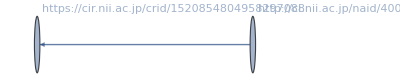
{20231010,{20,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{226815,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

{226815,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{205649,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{184333,3}

上が分離されたストーリー

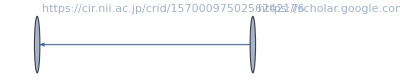
{20231010,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3[4][[1]]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
Directory[]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
(*Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]*)
```

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{184333}

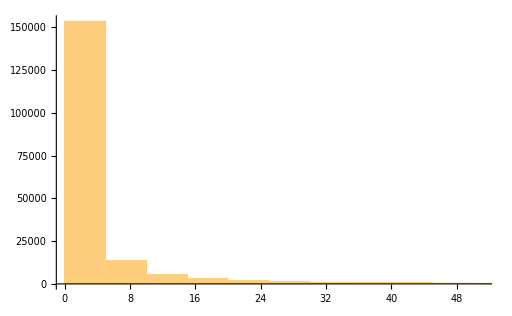

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{184333}

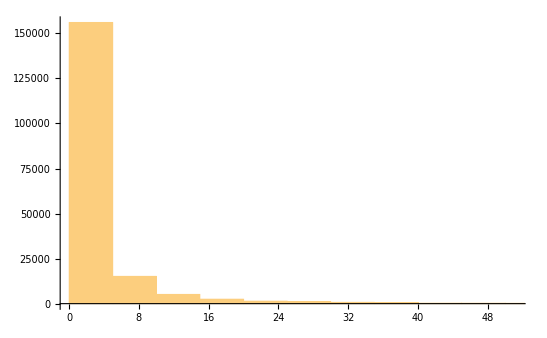

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{184333}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{184333}

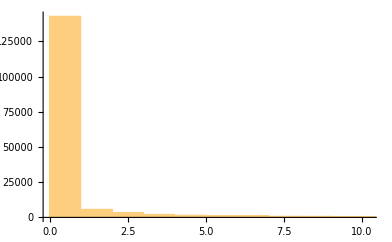

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{184333}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{184333}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{184333}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{184333}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{about:blank}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{41,55,56,71,74,95,97,124,157,207,225,251,252,256,270,319,328,343,408,409,463,467,508,660,699,760,762,766,870,872,877,911,913,914,1155,1164,1196,1539}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jupyter.cs.rcos.nii.ac.jp,http:kaken.nii.ac.jp,http:lms.nii.ac.jp,http:preview-jupyter.cs.rcos.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:contents.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:kurume.repo.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:njc.repo.nii.ac.jp,https:nrid.nii.ac.jp,https:openidp.nii.ac.jp,https:operationhub.cs.rcos.nii.ac.jp,https:otsuma.repo.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp,https:stars.repo.nii.ac.jp,https:support.nii.ac.jp,https:toyo-bunko.repo.nii.ac.jp,https:www.nii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{184333}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,163030},{1,21297},{3,6}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1806,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,137013},{2,47249},{0,69},{3,2}}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{49,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 136772
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20888
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 25280
https:cir.nii.ac.jp
https:support.nii.ac.jp | 107
https:cir.nii.ac.jp
https:www.nii.ac.jp | 10
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 104
 | 69
https:lms.nii.ac.jp | 143
https:jupyter.cs.rcos.nii.ac.jp
https:meatwiki.nii.ac.jp | 3
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 483
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 239
http:kaken.nii.ac.jp
https:cir.nii.ac.jp | 2
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 15
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 31
https:jupyter.cs.rcos.nii.ac.jp | 96
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 13
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 8
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:toyo-bunko.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kurume.repo.nii.ac.jp | 2
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 6
https:cir.nii.ac.jp
https:otsuma.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 4
https:redmine.devops.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:cir.nii.ac.jp
https:idp.nii.ac.jp | 1
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 13
https:jupyter.cs.rcos.nii.ac.jp
https:operationhub.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:contents.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:contents.nii.ac.jp
https:lms.nii.ac.jp | 2
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 2
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 8
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 2
https:cir.nii.ac.jp
https:stars.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:njc.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:openidp.nii.ac.jp | 1
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 3
https:cir.nii.ac.jp
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
http:preview-jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{121,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{16,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{121,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{121,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{5,32,7,42,19,104,5,33,2,4,9,6,13,2,6,17,2,6,11,51,2,25,24,99,88,85,19,9,2,39,37,7,13,57,23,9,49,17,38,215,198,10,24,23,26,71,19,22,22,21,7,9,20,25,67,6,17,13,12,11,15,21,11,276,280,272,26,32,8,6,31,189,185,192,3,11,11,44,45,46,14,31,24,24,23,37,106,105,111,106,40,41,45,6,89,14,16,13,5,312,312,318,11,15,2,6,46,45,2,12,22,8,5,2,20,19,295,325,296,296,15}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{33.,2865.,77.,1336.,355.,30117.,802.,8363.,0.,63.,2375.,87.,129.,0.,398.,424.,0.,845.,132.,939.,0.,2197.,2186.,28325.,28325.,28325.,809.,65.,0.,35263.,35243.,191.,1224.,2968.,1083.,135.,5853.,3134.,6724.,4130.,4020.,2001.,1352.,1337.,5001.,23452.,2040.,1440.,1428.,1428.,849.,174.,1783.,516.,15556.,359.,410.,1224.,11101.,11016.,341.,330.,34812.,24038.,28523.,23983.,19502.,3318.,30525.,1387.,1322.,23346.,15718.,15718.,15755.,437.,398.,14707.,14707.,16886.,531.,32477.,24369.,11254.,11254.,27442.,27437.,27293.,27446.,27293.,20280.,20342.,20280.,104.,24932.,2024.,2007.,1980.,78.,17635.,17635.,26961.,2223.,2059.,0.,17077.,35296.,35266.,0.,1288.,2939.,123.,114.,0.,645.,627.,8848.,8848.,8848.,8848.,331.}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{121,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{888,1},{5043,1},{6086,1},{8845,1},{8949,1},{9492,1},{12443,1},{12903,1},{16925,1},{23064,1},{23722,1},{23826,1},{25863,1},{26350,1},{27216,1},{29045,1},{30166,1},{32289,1},{32493,1},{41688,1},{42374,1},{42580,1},{42580,1},{44627,1},{44627,1},{44627,1},{45238,1},{46599,1},{50267,1},{51540,1},{51540,1},{54147,1},{55078,1},{55874,1},{55947,1},{58827,1},{58830,1},{58858,1},{58876,1},{60551,1},{60551,1},{60551,1},{61029,1},{61029,1},{61055,1},{61599,1},{61608,1},{62578,1},{62578,1},{62578,1},{62799,1},{62945,1},{63338,1},{65312,1},{66102,1},{69213,1},{70632,1},{71995,1},{71999,1},{71999,1},{78100,1},{78100,1},{78110,1},{79940,1},{79940,1},{79940,1},{80300,1},{81313,1},{83213,1},{86213,1},{89927,1},{91299,1},{91299,1},{91299,1},{94703,1},{98403,1},{98403,1},{99551,1},{99551,1},{99551,1},{100421,1},{101044,1},{101044,1},{101044,1},{101044,1},{101343,1},{101693,1},{101693,1},{101693,1},{101693,1},{102713,1},{102713,1},{102713,1},{103863,1},{104318,1},{104422,1},{104422,1},{104422,1},{104778,1},{105480,1},{105480,1},{105480,1},{107743,1},{107743,1},{108958,1},{114524,1},{116845,1},{116845,1},{137416,1},{137477,1},{144638,1},{144806,1},{147618,1},{148333,1},{150444,1},{150444,1},{151376,1},{151376,1},{151376,1},{151376,1},{151962,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{5,32,7,42,19,104,5,33,2,4,9,6,13,2,6,17,2,6,11,51,2,25,24,99,88,85,19,9,2,39,37,7,13,57,23,9,49,17,38,215,198,10,24,23,26,71,19,22,22,21,7,9,20,25,67,6,17,13,12,11,15,21,11,276,280,272,26,32,8,6,31,189,185,192,3,11,11,44,45,46,14,31,24,24,23,37,106,105,111,106,40,41,45,6,89,14,16,13,5,312,312,318,11,15,2,6,46,45,2,12,22,8,5,2,20,19,295,325,296,296,15}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{8,53,7,96,44,163,7,41,1,3,12,9,16,1,12,42,1,8,15,87,1,62,50,178,129,142,35,12,1,66,51,8,22,75,38,10,83,21,63,323,302,16,52,47,46,128,38,54,45,44,12,10,30,35,99,7,18,20,17,16,17,23,14,396,412,404,49,40,10,5,46,325,311,311,2,15,13,67,68,74,20,45,41,40,35,66,308,284,297,286,51,52,58,6,133,28,29,25,4,501,503,547,20,16,1,10,75,67,1,22,30,11,7,1,34,29,984,1113,986,989,29}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{121}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0.25,24.5333,0.333333,2.48333,0.9,263.133,11.95,114.967,0,0.85,37.8167,0.483333,0.35,0,5.83333,1.,0,10.95,0.733333,1.81667,0,11.3167,11.3167,264.483,421.583,421.583,3.01667,0.25,0,339.933,340.083,1.83333,5.7,13.3167,12.0833,0.75,18.6667,23.2,32.7333,17.3833,17.3833,26.9833,15.15,15.15,36.5833,328.417,17.9,5.23333,5.05,5.23333,7.73333,1.13333,16.05,1.06667,70.8167,4.35,2.63333,15.,167.317,167.317,1.48333,0.916667,341.633,188.233,187.583,188.267,209.1,11.85,505.65,21.7,3.31667,176.35,202.117,202.117,262.583,4.58333,4.58333,121.767,121.767,119.033,4.18333,352.983,218.4,81.2667,81.2667,313.05,59.95,59.95,38.4,59.95,99.0333,99.0333,92.5167,0.816667,369.283,19.55,19.55,19.55,0.9,77.1667,77.1667,92.6333,31.8333,26.9167,0,260.967,294.817,294.817,0,9.53333,10.4167,0.666667,0.716667,0,2.13333,2.61667,39.9167,39.9167,39.9167,39.9167,1.8}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{33.,2865.,77.,1336.,355.,30117.,802.,8363.,0.,63.,2375.,87.,129.,0.,398.,424.,0.,845.,132.,939.,0.,2197.,2186.,28325.,28325.,28325.,809.,65.,0.,35263.,35243.,191.,1224.,2968.,1083.,135.,5853.,3134.,6724.,4130.,4020.,2001.,1352.,1337.,5001.,23452.,2040.,1440.,1428.,1428.,849.,174.,1783.,516.,15556.,359.,410.,1224.,11101.,11016.,341.,330.,34812.,24038.,28523.,23983.,19502.,3318.,30525.,1387.,1322.,23346.,15718.,15718.,15755.,437.,398.,14707.,14707.,16886.,531.,32477.,24369.,11254.,11254.,27442.,27437.,27293.,27446.,27293.,20280.,20342.,20280.,104.,24932.,2024.,2007.,1980.,78.,17635.,17635.,26961.,2223.,2059.,0.,17077.,35296.,35266.,0.,1288.,2939.,123.,114.,0.,645.,627.,8848.,8848.,8848.,8848.,331.}

```mathematica
staytimeCKAN/60
```

{0.55,47.75,1.28333,22.2667,5.91667,501.95,13.3667,139.383,0.,1.05,39.5833,1.45,2.15,0.,6.63333,7.06667,0.,14.0833,2.2,15.65,0.,36.6167,36.4333,472.083,472.083,472.083,13.4833,1.08333,0.,587.717,587.383,3.18333,20.4,49.4667,18.05,2.25,97.55,52.2333,112.067,68.8333,67.,33.35,22.5333,22.2833,83.35,390.867,34.,24.,23.8,23.8,14.15,2.9,29.7167,8.6,259.267,5.98333,6.83333,20.4,185.017,183.6,5.68333,5.5,580.2,400.633,475.383,399.717,325.033,55.3,508.75,23.1167,22.0333,389.1,261.967,261.967,262.583,7.28333,6.63333,245.117,245.117,281.433,8.85,541.283,406.15,187.567,187.567,457.367,457.283,454.883,457.433,454.883,338.,339.033,338.,1.73333,415.533,33.7333,33.45,33.,1.3,293.917,293.917,449.35,37.05,34.3167,0.,284.617,588.267,587.767,0.,21.4667,48.9833,2.05,1.9,0.,10.75,10.45,147.467,147.467,147.467,147.467,5.51667}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.keiho-u.ac.jp/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{121}

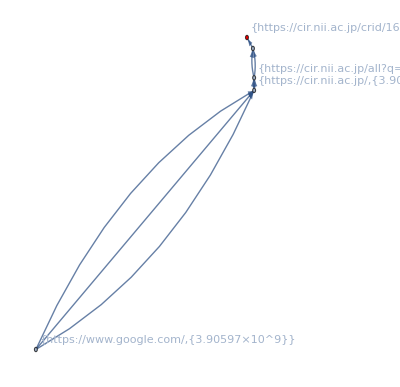
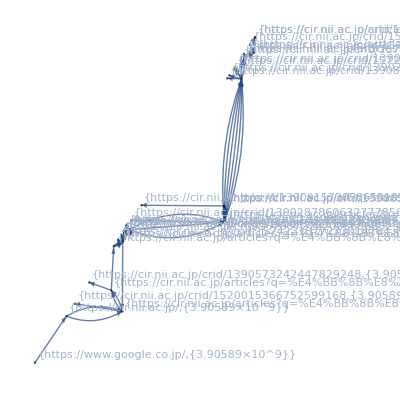
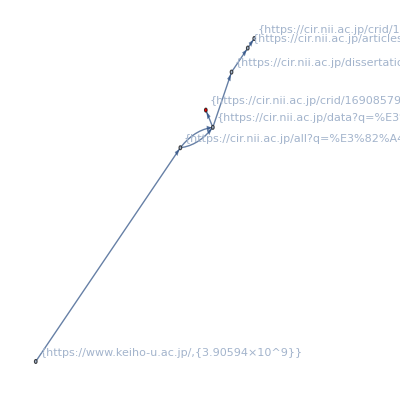
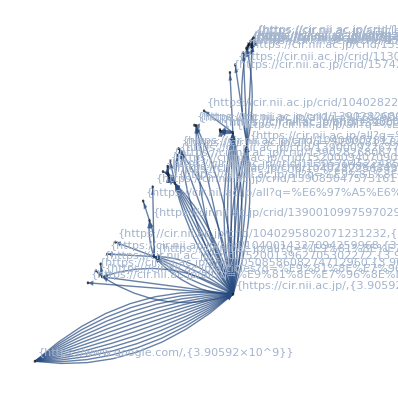
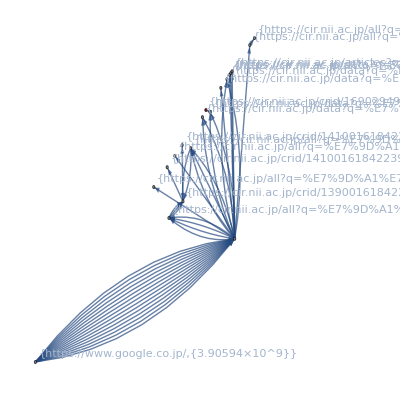
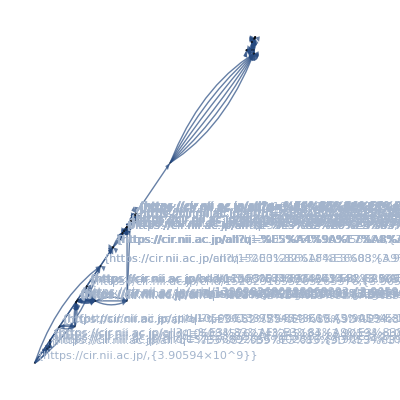
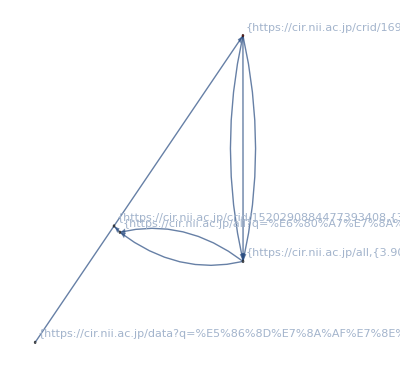
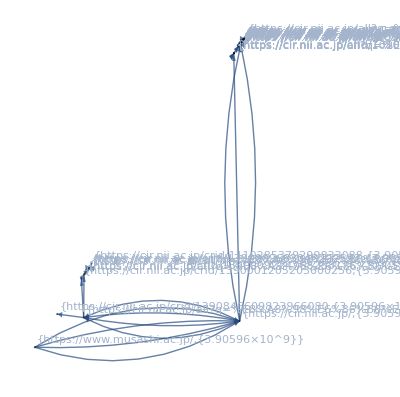
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 21124901
2962926

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 193
11
204 | 166
8
166

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 184333
121

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100
101
102
103
104
105
106
107
108
109
110
111
112
113
114
115
116
117
118
119
120
121 | 888 | 1
5043 | 1
6086 | 1
8845 | 1
8949 | 1
9492 | 1
12443 | 1
12903 | 1
16925 | 1
23064 | 1
23722 | 1
23826 | 1
25863 | 1
26350 | 1
27216 | 1
29045 | 1
30166 | 1
32289 | 1
32493 | 1
41688 | 1
42374 | 1
42580 | 1
42580 | 1
44627 | 1
44627 | 1
44627 | 1
45238 | 1
46599 | 1
50267 | 1
51540 | 1
51540 | 1
54147 | 1
55078 | 1
55874 | 1
55947 | 1
58827 | 1
58830 | 1
58858 | 1
58876 | 1
60551 | 1
60551 | 1
60551 | 1
61029 | 1
61029 | 1
61055 | 1
61599 | 1
61608 | 1
62578 | 1
62578 | 1
62578 | 1
62799 | 1
62945 | 1
63338 | 1
65312 | 1
66102 | 1
69213 | 1
70632 | 1
71995 | 1
71999 | 1
71999 | 1
78100 | 1
78100 | 1
78110 | 1
79940 | 1
79940 | 1
79940 | 1
80300 | 1
81313 | 1
83213 | 1
86213 | 1
89927 | 1
91299 | 1
91299 | 1
91299 | 1
94703 | 1
98403 | 1
98403 | 1
99551 | 1
99551 | 1
99551 | 1
100421 | 1
101044 | 1
101044 | 1
101044 | 1
101044 | 1
101343 | 1
101693 | 1
101693 | 1
101693 | 1
101693 | 1
102713 | 1
102713 | 1
102713 | 1
103863 | 1
104318 | 1
104422 | 1
104422 | 1
104422 | 1
104778 | 1
105480 | 1
105480 | 1
105480 | 1
107743 | 1
107743 | 1
108958 | 1
114524 | 1
116845 | 1
116845 | 1
137416 | 1
137477 | 1
144638 | 1
144806 | 1
147618 | 1
148333 | 1
150444 | 1
150444 | 1
151376 | 1
151376 | 1
151376 | 1
151376 | 1
151962 | 1 | 5
32
7
42
19
104
5
33
2
4
9
6
13
2
6
17
2
6
11
51
2
25
24
99
88
85
19
9
2
39
37
7
13
57
23
9
49
17
38
215
198
10
24
23
26
71
19
22
22
21
7
9
20
25
67
6
17
13
12
11
15
21
11
276
280
272
26
32
8
6
31
189
185
192
3
11
11
44
45
46
14
31
24
24
23
37
106
105
111
106
40
41
45
6
89
14
16
13
5
312
312
318
11
15
2
6
46
45
2
12
22
8
5
2
20
19
295
325
296
296
15 | 8
53
7
96
44
163
7
41
1
3
12
9
16
1
12
42
1
8
15
87
1
62
50
178
129
142
35
12
1
66
51
8
22
75
38
10
83
21
63
323
302
16
52
47
46
128
38
54
45
44
12
10
30
35
99
7
18
20
17
16
17
23
14
396
412
404
49
40
10
5
46
325
311
311
2
15
13
67
68
74
20
45
41
40
35
66
308
284
297
286
51
52
58
6
133
28
29
25
4
501
503
547
20
16
1
10
75
67
1
22
30
11
7
1
34
29
984
1113
986
989
29 | 0.25
24.5333
0.333333
2.48333
0.9
263.133
11.95
114.967
0
0.85
37.8167
0.483333
0.35
0
5.83333
1.
0
10.95
0.733333
1.81667
0
11.3167
11.3167
264.483
421.583
421.583
3.01667
0.25
0
339.933
340.083
1.83333
5.7
13.3167
12.0833
0.75
18.6667
23.2
32.7333
17.3833
17.3833
26.9833
15.15
15.15
36.5833
328.417
17.9
5.23333
5.05
5.23333
7.73333
1.13333
16.05
1.06667
70.8167
4.35
2.63333
15.
167.317
167.317
1.48333
0.916667
341.633
188.233
187.583
188.267
209.1
11.85
505.65
21.7
3.31667
176.35
202.117
202.117
262.583
4.58333
4.58333
121.767
121.767
119.033
4.18333
352.983
218.4
81.2667
81.2667
313.05
59.95
59.95
38.4
59.95
99.0333
99.0333
92.5167
0.816667
369.283
19.55
19.55
19.55
0.9
77.1667
77.1667
92.6333
31.8333
26.9167
0
260.967
294.817
294.817
0
9.53333
10.4167
0.666667
0.716667
0
2.13333
2.61667
39.9167
39.9167
39.9167
39.9167
1.8 | 0.55
47.75
1.28333
22.2667
5.91667
501.95
13.3667
139.383
0.
1.05
39.5833
1.45
2.15
0.
6.63333
7.06667
0.
14.0833
2.2
15.65
0.
36.6167
36.4333
472.083
472.083
472.083
13.4833
1.08333
0.
587.717
587.383
3.18333
20.4
49.4667
18.05
2.25
97.55
52.2333
112.067
68.8333
67.
33.35
22.5333
22.2833
83.35
390.867
34.
24.
23.8
23.8
14.15
2.9
29.7167
8.6
259.267
5.98333
6.83333
20.4
185.017
183.6
5.68333
5.5
580.2
400.633
475.383
399.717
325.033
55.3
508.75
23.1167
22.0333
389.1
261.967
261.967
262.583
7.28333
6.63333
245.117
245.117
281.433
8.85
541.283
406.15
187.567
187.567
457.367
457.283
454.883
457.433
454.883
338.
339.033
338.
1.73333
415.533
33.7333
33.45
33.
1.3
293.917
293.917
449.35
37.05
34.3167
0.
284.617
588.267
587.767
0.
21.4667
48.9833
2.05
1.9
0.
10.75
10.45
147.467
147.467
147.467
147.467
5.51667

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{121}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{121}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.908610394722913×10^9

```mathematica
end-start
```

928.703906